# Holografie-Funktion: Kurvendiskussion

Dieses Worksheet sammelt einfache Plots zum Einbinden und stellt Zusammenhänge nochmal her, die ich immer wieder vergesse.

## Einführung

Nochmal ganz, ganz... ausführlich. Die Holo-Funktion und ihre Ableitung in 1d, ohne Vorfaktoren.

```mathematica
h[z_]=1/(1+1/z^2)
```

1/(1+1/z^2)

```mathematica
dh[z_]=D[h[z],z]
```

2/((1+1/z^2)^2 z^3)

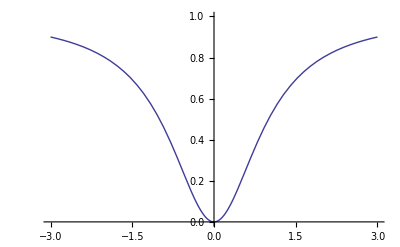

```mathematica
Plot[h[z],{z,-3,3},PlotRange->{0,1}]
```

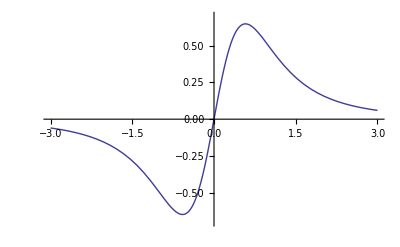

```mathematica
Plot[dh[z],{z,-3,3},PlotRange->{-1,1}*0.7]
```

## Darstellung mit z und r im Unterschied

Der 1/(1+(1/z)^...)-Term stellt die numerische Auswertung vor Probleme. Stellt man den Term anders (eben mit r^../(r^... + 1) dar, gibt es diese Probleme nicht. Dies zeigt dieser Abschnitt. Beide Darstellungen sind natürlich identisch, wie auch die Serienzerlegung zeigt.

```mathematica
(* Fehler - sic! *)
dh[0]
```

Power::infy: Infinite expression 1/0^2 encountered.

Power::infy: Infinite expression 1/0^3 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Indeterminate

```mathematica
(* Im LImes wohldefiniert *)
Limit[dh[z],z-> 0]
```

0

```mathematica
(* In seiner gewoehnlichen Darstellung *)
dhx[x_] = D[x^2 / (x^2 + 1), x] // FullSimplify
```

(2 x)/((1+x^2)^2)

```mathematica
(* Das funktioniert problemlos *)
dhx[0]
```

0

```mathematica
(* Gleiche Serienentwicklung *)
Series[dh[z],{z,0,10}]
Series[dhx[x],{x,0,10}]
```

2 z-4 z^3+6 z^5-8 z^7+10 z^9+O[z]^11

2 x-4 x^3+6 x^5-8 x^7+10 x^9+O[x]^11

```mathematica
(* Auch gleiche Nenner - bemerke, 1/z sort fuer die Divergenz *)
Series[2/dh[z],{z,0,10}]
Series[2/dhx[x],{x,0,10}]
```

1/z+2 z+z^3+O[z]^11

1/x+2 x+x^3+O[x]^11

## Höherdimensional: Das A-Integral

Das A(p)-Integral sorgt immer wieder für Verwirrung. Zwei Wochen lang ging ich jeden Tag davon aus, die resultierende Funktion wäre assymmetrisch. Dies ist falsch, wie sich mir erst heute am 5. Mai mal wieder offenbarte.

```mathematica
Dhn[z_,n_] = D[z^(2+n)/(z^(2+n) + 1), z];
Fun[z_,n_] = z^(1+n) * Dhn[Abs[z],n]
```

z^(1+n) (-((2+n) Abs[z]^(3+2 n))/((1+Abs[z]^(2+n))^2)+((2+n) Abs[z]^(1+n))/(1+Abs[z]^(2+n)))

So sieht das Ding in 4d aus:

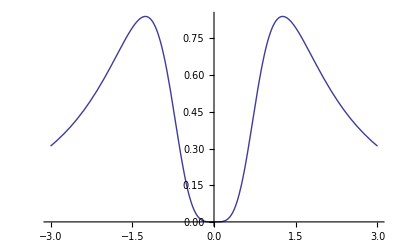

```mathematica
Plot[Fun[z,1],{z,-3,3}]
```

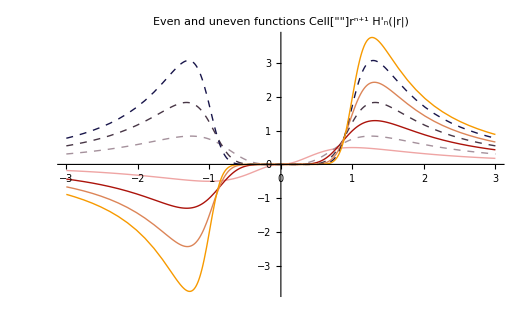

```mathematica
Plot[Table[Fun[z,n],{n,0,6}]//Evaluate,
{z,-3,3}, 
PlotStyle->(Riffle[#,{Dashed,#}&/@Reverse[#]]& [ColorData[9,"ColorList"]]),
PlotLabel -> "Even and uneven functions Cell[""]r^(n+1)H'_n(|r|)"
]
```